# Tyler’s Three Bessel Function Solution

```mathematica
bwm[h_Real?NumericQ]:=2.5+18.5*Exp[-(((h/1000.0)-12.0)^2.0)/25.0]
```

```mathematica
A[h_]:= 10.^((-9.401-1.5913*(h/1000.0)-0.0606*(h/1000.0)^2.0));
B[h_]:=10.^(-17.1273-0.0332*(h/1000.0) - 0.0015*(h/1000.0)^2 + 0.9061*Exp[-0.5*((15.0866-(h/1000.0))/5.2977)^2])
Maui[h_Real?NumericQ]:=Piecewise[{{A[h],3.048*^3<h<=4.2*^3},{B[h],4.2*^3<h<=25.0*^3},{B[h]*Exp[-((h/1000.0)-25.0)/5.0],h> 25.0*^3}}]
```

```mathematica
C1[γ_]:= ((2*Gamma[1./2]*Gamma[1./2-γ/2.0])/(5 Gamma[γ]));
```

```mathematica
C2[γ_]:=-π^(-(γ+2))(Gamma[(γ+3)/2]/Gamma[-(γ+1)/2])
```

```mathematica
R=1.5;
λ=1.0*^-6;
k=2*π/λ;
```

```mathematica
G110Large[γ_,β_]:=(2^(-4-γ) β^(1+γ) Gamma[1/2 (-1-γ)] HypergeometricPFQ[{3/2,-1/2-γ/2,-1/2-γ/2},{2,3},4/β^2])/Gamma[(3+γ)/2]
```

```mathematica
G110Small[γ_,β_]:=(2^(-5-γ) β^(4+γ) Gamma[1/2 (-4-γ)] HypergeometricPFQRegularized[{3/2,-1/2,1/2},{(6+γ)/2,(6+γ)/2},β^2/4])/(π^(3/2) Gamma[(6+γ)/2])+(2^(-4-γ) Gamma[1/2 (-1-γ)] Gamma[4+γ] HypergeometricPFQRegularized[{1/2 (-1-γ),1/2 (-5-γ),1/2 (-3-γ)},{1,1/2 (-2-γ)},β^2/4])/(Gamma[1/2 (-3-γ)] Gamma[(5+γ)/2]^2 Gamma[(7+γ)/2])
```

```mathematica
Garg[γ_,β_]:= Piecewise[ {{G110Small[γ,0]-G110Small[γ,β],β<=2},{G110Small[γ,0]-G110Large[γ,β],β>2}}]
```

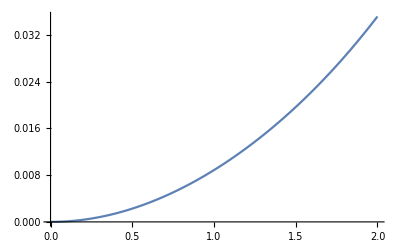

```mathematica
Plot[Garg[0.333,t],{t,0,2}]
```

```mathematica
DP[τ_,γ_]:=k^2 R^(-γ-3)(2π)^(-γ-2)C1[γ]*C2[γ]*NIntegrate[Maui[h]*Garg[γ,bwm[h]*τ/R],{h,3300.0,30000.0}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in h near {h} = {4215.537904228081970359198749065399169921875}. NIntegrate obtained 4.17848×10^-22 and 5.67496×10^-28 for the integral and error estimates.

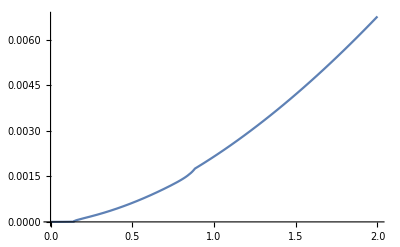

```mathematica
Plot[DP[t,0.666],{t,0,2}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in h near {h} = {4215.537904228081970359198749065399169921875}. NIntegrate obtained 1.34019×10^-22 and 1.81956×10^-28 for the integral and error estimates.

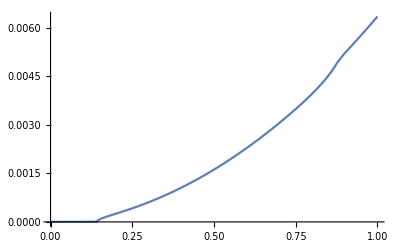

```mathematica
Plot[DP[t,0.9],{t,0,1}]
```

```mathematica
resultOK= Union[ParallelTable[Quiet@DP[τ,0.666],{τ,0.0,1.0,1.0*^-2}],ParallelTable[Quiet@DP[τ,0.666],{τ,1.0,2.0,1/100}]];
```

```mathematica
resultNOKH= Union[ParallelTable[Quiet@DP[τ,0.9],{τ,0.0,1.0,1.0*^-2}],ParallelTable[Quiet@DP[τ,0.9],{τ,1.0,2.0,1/100}]];
resultNOKL= Union[ParallelTable[Quiet@DP[τ,0.1],{τ,0.0,1.0,1.0*^-2}],ParallelTable[Quiet@DP[τ,0.1],{τ,1.0,2.0,1/100}]];
```

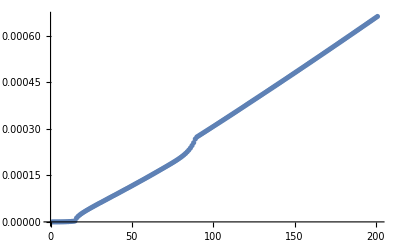

```mathematica
ListPlot[{resultNOKL}]
```

```mathematica
Export["TylerBesselThree_NOK_High_result.csv",resultNOKH]
```

TylerBesselThree_NOK_High_result.csv

```mathematica
Export["TylerBesselThree_NOK_Low_result.csv",resultNOKL]
```

TylerBesselThree_NOK_Low_result.csv

```mathematica
Export["TylerBesselThree_OK_result.csv",resultOK]
```

TylerBesselThree_OK_result.csv